```mathematica
EC = ComplexExpand[(((p + I q)(X + I Y) + a X - I b Y))(X'+ I Y')]
```

a X X'+p X X'-q Y X'-q X Y'+b Y Y'-p Y Y'+ⅈ (q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')

```mathematica
a X X'+p X X'-q Y X'-q X Y'+b Y Y'-p Y Y'+ⅈ (q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')
```

a X X'+p X X'-q Y X'-q X Y'+b Y Y'-p Y Y'+ⅈ (q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')

```mathematica
Eq = q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y';
```

```mathematica
Eq1 =((Eq/.{X'-> D[E^f[θ]Cos[θ],θ], Y'->D[E^f[θ]Sin[θ],θ],X ->E^f[θ]Cos[θ],Y ->E^f[θ]Sin[θ]})/E^(2f[θ]))//Simplify
```

1/2 (a+b+(a-b+2 p) Cos[2 θ]-2 q Sin[2 θ]+(2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]) f'[θ])

```mathematica
lr = (f[θ]/.DSolve[Eq1==0,f[θ],θ][[1]])/.{C[1]->0}
```

-((2 (a+b) ArcTanh[(-a+b-2 p+2 q Tan[θ])/(√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2))]+√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2) Log[2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]])/(2 √(a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2+q^2))))

```mathematica
Sub[α_, β_,a_,c_] :=
{
H ->  -c/(2α )Cos[2β],
q -> -c/(4 α) Sin[2β],
p ->(b - a - H)/2,
b -> - a-c
};
```

```mathematica
lfs=FullSimplify[lr//.Sub[α,β, a,c],{c>0,μ>1} ]
```

-2 α ArcTanh[Cos[2 β-θ] Sec[θ]]-1/2 Log[-(c Sin[2 β-2 θ])/(2 α)]

```mathematica
collectLog[expr_]:=Module[{rule1,rule2,rule3,a,b,x},
rule1=Log[a_]+Log[b_]:>Log[a*b];
rule2=x_*Log[a_]:>Log[a^x];
rule3 = x_ ArcTanh[a_] :> Log[(1 + a)^(x/2) (1-a)^(-x/2)];
expr//.{rule1,rule2,rule3}
];
```

```mathematica
r[θ_] :=Simplify[Sqrt[c/(2 α)] Exp[collectLog[lfs]]/.Exp[Log[x_]] ->x,{c >0, α>0}]
```

```mathematica
r[θ]
```

((Sec[θ] Sin[β] Sin[β-θ])^α (Cos[β] (Cos[β]+Sin[β] Tan[θ]))^-α)/(√(-Sin[2 β-2 θ]))

```mathematica
TrigReduce[Cos[θ](1-Cos[β])-Sin[β] Sin[θ]]/Cos[θ]
```

(-Cos[β-θ]+Cos[θ]) Sec[θ]

```mathematica
TrigReduce[Cos[θ](1+Cos[β])+Sin[β] Sin[θ]]/Cos[θ]
```

(Cos[β-θ]+Cos[θ]) Sec[θ]

```mathematica
R0[θ_] =(-(Cos[θ]-Cos[2β-θ])/(Cos[θ] +Cos[2β-θ]) )^α/√(-Sin[2β-2 θ])
```

((Cos[2 β-θ]-Cos[θ])/(Cos[2 β-θ]+Cos[θ]))^α/(√(-Sin[2 β-2 θ]))

```mathematica
R1[θ_] =R0[θ + β]//FullSimplify
```

(Tan[β] Tan[θ])^α/(√Sin[2 θ])

```mathematica
FullSimplify[R1[θ]^2/.α->1/2]
```

Csc[2 θ] Tan[β] Tan[θ]

```mathematica
FullSimplify[Sqrt[2Cancel[( Sin[θ]/Cos[θ])^(2 n +1)/(2 Sin[θ] Cos[θ])]], {0 < θ < Pi/2, n  >= 0}]
```

Sec[θ] Tan[θ]^n

```mathematica
1/2 Sec[θ]^2 Tan[β]
```

1/2 Sec[θ]^2 Tan[β]

```mathematica
(* switchingb to τ = Tan[θ] *)
```

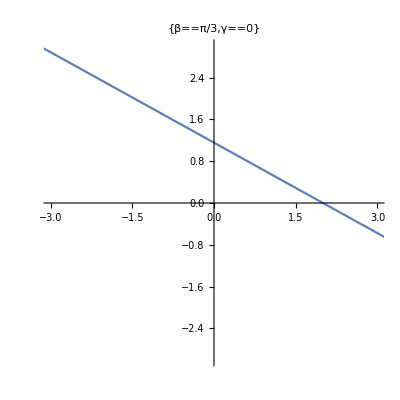

```mathematica
With[{β=Pi/3},ParametricPlot[ReIm[(1 + I τ) Exp[I  β]],{τ,-10,10},PlotLabel->{Symbol["β"]==β,Symbol["γ"]==0},PlotRange->{{-3,3},{-3,3}}]]
```

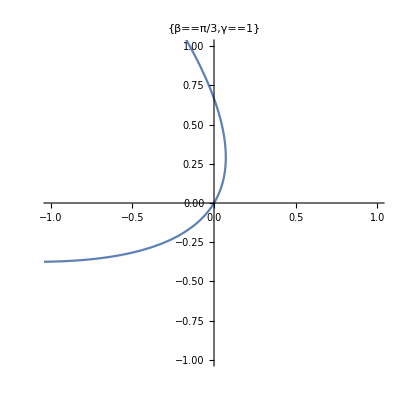

```mathematica
With[{β=Pi/3},ParametricPlot[ReIm[(1 + I τ) τ Exp[I  β]],{τ,-10,10},PlotLabel->{Symbol["β"]==β,Symbol["γ"]==1},
PlotRange->{{-1,1},{-1,1}}]]
```

```mathematica
With[{β=Pi/3},ParametricPlot[ReIm[(1 + I τ) τ^2 Exp[I  β/2]],{τ,-3,3},{θ,-Pi, +Pi},PlotLabel->{Symbol["β"]==β,Symbol["γ"]==2},
MaxRecursion->4,
PlotRange->{{-1,1},{-1,1}}]]
```

-Graphics-

```mathematica
With[{β=Pi/3},ParametricPlot[ReIm[(1 + I τ) τ^3 Exp[I  β]],{τ,-3,3},{θ,-Pi, +Pi},PlotLabel->{Symbol["β"]==β,Symbol["γ"]==3},
MaxRecursion->4,
PlotRange->{{-1,1},{-1,1}}]]
```

-Graphics-

```mathematica
EtaSub[β_,τ_,n_]:= 
{η-> (1 + I τ) τ^n Exp[I  β],
η*->(1 - I τ) τ^n Exp[-I  β]};
```

```mathematica
F[ζ_,β_,a_,c_,n_] :=FullSimplify[(-(p+ 2a+c + I q )η + c η*)/.EtaSub[β, ζ,n]//.Sub[n+1/2, β,a,c] ]
```

```mathematica
F[τ,β,a,c,2 k +1]/.(-ⅈ Cos[x_]+Sin[x_]):>-I Exp[I x]//FullSimplify
```

1/2 ⅇ^(-ⅈ β) τ^(1+2 k) (-ⅈ (2 a+c) ⅇ^(2 ⅈ β) (-ⅈ+τ)+(c (5+8 k-ⅈ (7+8 k) τ))/(3+4 k))

```mathematica
Eta[τ_,β_,n_]:= η/.EtaSub[β,τ,n]
```

```mathematica
Eta[τ,β,2 k +1]
```

ⅇ^(ⅈ β) (1+ⅈ τ) τ^(1+2 k)

```mathematica
Solve[D[Eta[τ,β,2 k +1],τ]==0,τ]
```

{{τ→(ⅈ (1+2 k))/(2 (1+k))}}

```mathematica
BB=FullSimplify[Limit[F[τ,β,a,c,2 k +1]/Eta[τ,β,2 k +1],τ->Infinity]]
```

-a+1/2 c (-1-(ⅇ^(-2 ⅈ β) (7+8 k))/(3+4 k))

```mathematica
V=FullSimplify[ReIm[ComplexExpand[a x - I(c+a) y +ExpToTrig[Conjugate[BB (x + I y)]]]],{{a,c,x,y,k,β} ∈ Reals, 1/(6 + 8 k) >0}]
```

{-(c ((3+4 k) x+(7+8 k) x Cos[2 β]+(7+8 k) y Sin[2 β]))/(6+8 k),(c (-((3+4 k) y)+(7+8 k) y Cos[2 β]-(7+8 k) x Sin[2 β]))/(6+8 k)}

```mathematica
M = Grad[V,{x,y}]
```

{{-(c (3+4 k+(7+8 k) Cos[2 β]))/(6+8 k),-(c (7+8 k) Sin[2 β])/(6+8 k)},{-(c (7+8 k) Sin[2 β])/(6+8 k),(c (-3-4 k+(7+8 k) Cos[2 β]))/(6+8 k)}}

```mathematica
S=(M + Transpose[M])/2
```

{{-(c (3+4 k+(7+8 k) Cos[2 β]))/(6+8 k),-(c (7+8 k) Sin[2 β])/(6+8 k)},{-(c (7+8 k) Sin[2 β])/(6+8 k),(c (-3-4 k+(7+8 k) Cos[2 β]))/(6+8 k)}}

```mathematica
MatrixForm[S]
```

(-(c (3+4 k+(7+8 k) Cos[2 β]))/(6+8 k) | -(c (7+8 k) Sin[2 β])/(6+8 k)
-(c (7+8 k) Sin[2 β])/(6+8 k) | (c (-3-4 k+(7+8 k) Cos[2 β]))/(6+8 k))

```mathematica
Eigenvalues[S]
```

{(2 c (1+k))/(3+4 k),-(c (5+6 k))/(3+4 k)}

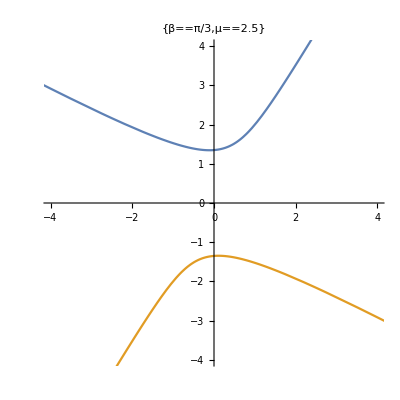

```mathematica
With[{β=Pi/3},ParametricPlot[{ReIm[(τ + I τ^(-2.5))  Exp[I  β]],ReIm[-(τ + I τ^(-2.5)) Exp[I  β]]},{τ,0.1,10},PlotLabel->{Symbol["β"]==β,Symbol["μ"]==2.5},
PlotRange->{{-4,4},{-4,4}}]]
```

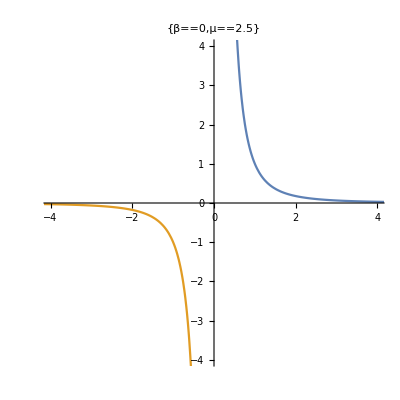

```mathematica
With[{β=0},ParametricPlot[{ReIm[(τ + I τ^(-2.5))  Exp[I  β]],ReIm[-(τ + I τ^(-2.5)) Exp[I  β]]},{τ,0.1,10},PlotLabel->{Symbol["β"]==β,Symbol["μ"]==2.5},
PlotRange->{{-4,4},{-4,4}}]]
```

```mathematica
EtaSubHyper[β_,ξ_,μ_]:= 
{η-> (ξ + I ξ^(-μ))  Exp[I  β],
η*->(ξ - I ξ^(-μ)) Exp[-I  β]};
```

```mathematica
FHyper[ξ_,β_,a_,c_,μ_] :=FullSimplify[(-(p+ 2a+c + I q )η + c η*)/.EtaSubHyper[β, ξ,μ]//.Sub[(μ-1)/(2(μ+1)), β,a,c] ]
```

```mathematica
EtaHyper[β_,ξ_,μ_] := (η/.EtaSubHyper[β,ξ,μ])

EtaHyper[β,ξ,μ]
```

ⅇ^(ⅈ β) (ξ+ⅈ ξ^-μ)

```mathematica
FullSimplify /@Collect[FHyper[ξ,β,a,c,μ] ,{ξ,ξ^(-μ)}]
```

1/2 ⅇ^(-ⅈ β) (-((2 a+c) ⅇ^(2 ⅈ β))+(c (-3+μ))/(-1+μ)) ξ-(ⅈ ⅇ^(-ⅈ β) ((2 a+c) ⅇ^(2 ⅈ β) (-1+μ)+c (-1+3 μ)) ξ^-μ)/(2 (-1+μ))

```mathematica
FullSimplify[Solve[D[EtaHyper[β,ξ,μ],ξ]==0,ξ][[1]],μ>1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ξ→(ⅈ μ)^(1/(1+μ))}

```mathematica
BB=FullSimplify[Coefficient[FHyper[ξ,β,a,c,μ],ξ]/Coefficient[EtaHyper[β,ξ,μ],ξ]]
```

-a+1/2 c (-1+(ⅇ^(-2 ⅈ β) (-3+μ))/(-1+μ))

```mathematica
Solve[(BB/.β->0)==0,μ][[1]]
```

{μ→(a-c)/a}

```mathematica
Solve[(BB/.β->Pi/2)==0,μ][[1]]
```

{μ→(a+2 c)/(a+c)}

```mathematica
asol = Solve[a μ == a-c,a][[1]]
```

{a→-c/(-1+μ)}

```mathematica
μ1 = (1 + c/(-c+a))/.asol//Simplify
```

1/μ